# Числено интергриране. Квадратурни формули на Нютон-Коутс

## ∫_6^7 (Sin[x+3]^2)^(1/7)ⅆx 1. Съставяне на мрежа: a = 6; b = 7 Вариант за съставяне: 1.1 Даден е h => n = (b -a)/h 1.2 Даден е n => h = (b-a)/n 1.3 Даден е броя на възлите n+1 => n => h x_i = a + i * h, i = OverBar[0,n]

## Вградените възможности на Wolfram

```mathematica
∫_6^7 (Sin[x+3]^2)^(1/7)ⅆx
```

7/9 (Hypergeometric2F1[1/2,9/14,23/14,Sin[9]^2] Sin[9]^(9/7)+Hypergeometric2F1[1/2,9/14,23/14,Sin[10]^2] (-Sin[10])^(9/7))

```mathematica
%//N
```

0.637467

За по-сложна функция

```mathematica
∫_6^7 ((Sin[x+3]^2)^(1/7))/Tanh[ⅇ^3] ⅆx
```

7/9 Coth[ⅇ^3] (Hypergeometric2F1[1/2,9/14,23/14,Sin[9]^2] Sin[9]^(9/7)+Hypergeometric2F1[1/2,9/14,23/14,Sin[10]^2] (-Sin[10])^(9/7))

```mathematica
∫_6^7 ((Sin[x+3]^2)^(1/7))/(Tanh[ⅇ^3] * (√Cos[x^2])/(2x))ⅆx
```

∫_6^7 (2 x Coth[ⅇ^3] (Sin[3+x]^2)^(1/7))/(√Cos[x^2])ⅆx

```mathematica
∫_6^7 ((Sin[x+3]^2)^(1/7))/(Tanh[ⅇ^3] * (√Cos[x^2])/(2x))ⅆx //N
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.01176299523518}. NIntegrate obtained 7.57483-7.12394 ⅈ and 0.586182 for the integral and error estimates.

7.57483-7.12394 ⅈ

## Съставяне на мрежата

```mathematica
a = 7.; b =8;
h = 0.1;
n = (b-a)/h;
```

```mathematica
Table[a + i*h, {i, 0,n}]
```

{7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.}

## Леви правоъгълници

```mathematica
f[x_] := (Sin[x+3]^2)^(1/7)
Itochno =∫_a^b f[x]ⅆx //N (*за сравнение*)
I1 = h * ∑_(i=0)^(n-1) f[a + i*h]
```

0.618496

0.941444

### Оценка на грешката

#### Теоретична грешка

Намираме M_1

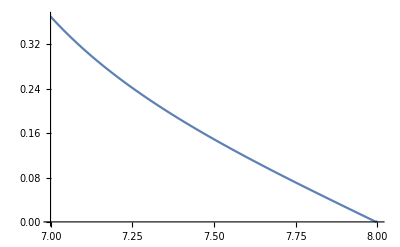

```mathematica
Plot[Abs[f'[x]], {x,a,b}]
```

```mathematica
M1 = Abs[f'[a]]
```

0.37032

```mathematica
R1 = (b-a)^2/(2n) * M1
```

0.018516

#### Истинска грешка

```mathematica
Abs[I1 - Itochno]
```

0.322949

### Групираме всичко в една клетка

```mathematica
a = 7.; b =8;
h = 0.1;
n = (b-a)/h;
f[x_] := (Sin[x+3]^2)^(1/7)
Itochno =∫_a^b f[x]ⅆx //N; (*за сравнение*)
I1 = h * ∑_(i=0)^(n-1) f[a + i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n) * M1;
Print["Мрежата е със стъпка ", h , " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1 - Itochno]]
```

Мрежата е със стъпка 0.1 и брой подинтервали 10.

Приближената стойност по формулата на левите правоъгълници е 0.941444

Точната стойност                                           е 0.618496

Теоретичната грешка по формулата на левите правоъгълници   е 0.018516

Истинската грешка по формулата на левите правоъгълници     е 0.322949

Извод: Имаме несъответствие между истинската и теоретичната грешка. Това се получава заради липса на гладкост на избраната подинтегрална функция.

Използваме друга функция за примерите.

## Трапеци

Намираме M_2

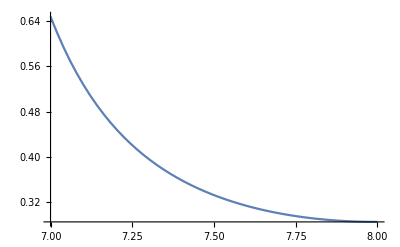

```mathematica
Plot[Abs[f''[x]], {x,a,b}]
```

```mathematica
a = 7.; b =8;
h = 0.1;
n = (b-a)/h;
f[x_] := (π Sin[x])/(x^2 + 2)
Itochno =∫_a^b f[x]ⅆx //N; (*за сравнение*)
IT = h/2 *(f[a] + 2 ∑_(i=1)^(n-1) f[a + i*h] + f[b]);
M2 = Abs[f''[a]];
RT = (b-a)^3/(12 n^2) * M2;
Print["Мрежата е със стъпка ", h , " и брой подинтервали ", n]
Print["Приближената стойност по формулата на трапците е ", IT]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на трапците   е ", RT]
Print["Истинската грешка по формулата на трапците     е ", Abs[IT - Itochno]]
```

Мрежата е със стъпка 0.1 и брой подинтервали 10.

Приближената стойност по формулата на трапците е 0.0482622

Точната стойност                               е 0.0483069

Теоретичната грешка по формулата на трапците   е 0.0000512122

Истинската грешка по формулата на трапците     е 0.0000447328

## Симпсън

Изискване за прилагане на формулата е броят на подинтервалите да е четно число

Намираме M_4

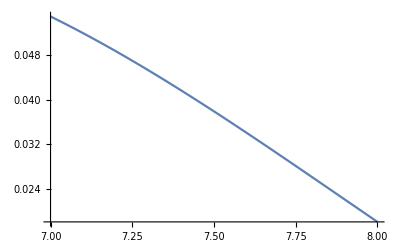

```mathematica
Plot[Abs[f''''[x]], {x,a,b}]
```

```mathematica
a = 7.; b =8;
h = 0.1;
n = (b-a)/h;
m = n/2;
f[x_] := (π Sin[x])/(x^2 + 2)
Itochno =∫_a^b f[x]ⅆx //N; (*за сравнение*)
IS = h/3 *(f[a] + 4 ∑_(i=1)^m f[a + (2i -1)*h] + 2 ∑_(i=1)^(m-1) f[a + (2i)*h]+ f[b]);
M4 = Abs[f''''[a]];
RS = (b-a)^5/(180 n^4) * M4;
Print["Мрежата е със стъпка ", h , " и брой подинтервали ", n]
Print["Приближената стойност по формулата на Симпсън  е ", IS]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на Симпсън    е ", RS]
Print["Истинската грешка по формулата на Симпсън      е ", Abs[IS - Itochno]]
```

Мрежата е със стъпка 0.1 и брой подинтервали 10.

Приближената стойност по формулата на Симпсън  е 0.0483069

Точната стойност                               е 0.0483069

Теоретичната грешка по формулата на Симпсън    е 3.05089×10^-8

Истинската грешка по формулата на Симпсън      е 2.07853×10^-8

## Пресмятане с предварително зададена грешка

## Леви правоъгълници

Определяме мрежата, n=?

```mathematica
f[x_] :=  (π Sin[x])/(x^2 + 2)
```

```mathematica
(*Намираме Subscript[M, 4]*)
```

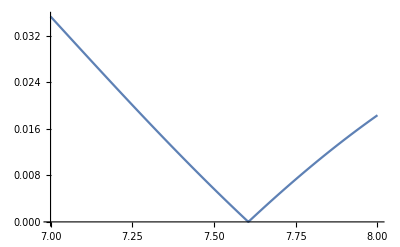

```mathematica
Plot[Abs[f'[x]], {x,a,b}]
```

```mathematica
M1 = Abs[f'[a]]
```

0.0353308

```mathematica
eps = 10^-8;
Clear[n]
Reduce [(b-a)^2/(2n) * M1 <= eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.76654×10^6

```mathematica
a = 7.; b =8;
n = 1.77 * 10^6;
h = (b-a)/n;
f[x_] :=(π Sin[x])/(x^2 + 2)
Itochno =∫_a^b f[x]ⅆx //N; (*за сравнение*)
I1 = h * ∑_(i=0)^(n-1) f[a + i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n) * M1;
Print["Мрежата е със стъпка ", h , " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1 - Itochno]]
```

Part::pspec1: Part specification KeyAbsent is not applicable.

Append::normal: Nonatomic expression expected at position 1 in Append[KeyAbsent,Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1]].

Part::pkspec1: The expression Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1] cannot be used as a part specification.

Append::argt: Append called with 3 arguments; 1 or 2 arguments are expected.

Part::pkspec1: The expression Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1] cannot be used as a part specification.

Append::argt: Append called with 4 arguments; 1 or 2 arguments are expected.

Part::pkspec1: The expression Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Append::argt: Append called with 5 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Append::argt will be suppressed during this calculation.

Part::pspec1: Part specification KeyAbsent is not applicable.

Append::normal: Nonatomic expression expected at position 1 in Append[KeyAbsent,Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1]].

MapAt::psl: Position specification Append[KeyAbsent,Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],Switch[Missing[KeyAbsent,Source],_List,None,_After,-1,_Before,1],«991»] in … is not a machine-sized integer or a list of machine-sized integers.